## Function definitions

### Various definitions of h(i_in)

```mathematica
hAccurate[iin_,β0_,βf_]=Integrate[1/(-im +1/2 im^2+iin),{im,β0,βf},Assumptions-> iin>0.5,GenerateConditions->False]
hLoAccurate[iin_,β0_]=Integrate[1/(-im +1/2 im^2+iin),{im,β0,∞},Assumptions-> iin>0.5,GenerateConditions->False]
hHiAccurate[iin_,βf_]=Integrate[1/(-im +1/2 im^2+iin),{im,0,βf},Assumptions-> iin>0.5,GenerateConditions->False]
hApprox[iin_]=Integrate[1/(-im +1/2 im^2+iin),{im,0,∞},Assumptions-> iin>0.5,GenerateConditions->False]
```

(2 (tan^-1((βf-1)/(√(2 iin-1)))-tan^-1((β0-1)/(√(2 iin-1)))))/(√(2 iin-1))

(π-2 tan^-1((β0-1)/(√(2 iin-1))))/(√(2 iin-1))

(2 (tan^-1((βf-1)/(√(2 iin-1)))+cot^-1(√(2 iin-1))))/(√(2 iin-1))

(2 cot^-1(√(2 iin-1))+π)/(√(2 iin-1))

### Definition of general firing rate equation

f=1/(τ h(i_in)); τ=ρ_tau/I_lkand h(i_in) is expanded as per hApprox above and where i_in=(I_in I_lk)/(I_lk+ρ_ilkr)^2

```mathematica
fireR[Iin_,Ilk_,pqua_,ptau_,pilkr_]:=(Ilk √(2 pqua (Iin Ilk)/(Ilk+pilkr)^2-1))/(ptau (π+2ArcCot[√(2 pqua (Iin Ilk)/(Ilk+pilkr)^2-1)]))
```

## Reset accuracy comparisons of h(i_in)

This section compares the various forms of h(i_in) that result from integrating to different bounds.  h_approx is the function that the general theory was evaluated for.  It assumes that the integral goes from 0 to ∞.  h_accurateis the fully accurate model which goes from some actual lower bound reset current value to the upper bound reset threshold.  These two bounds are labeled as i_m0 and i_mf.  h_loAccurateis the model which goes from i_m0 to ∞, which implies that the error is caused by approximating the upper bound threshold as ∞.  h_hiAccurate is the model which goes from 0 to i_mf, which implies that the error is caused by approximating the lower bound reset current as 0 instead of i_m0.

### General manipulator to compute the accuracy comparisons

```mathematica
imSz=Large;
Manipulate[
Grid[
{{
Plot[
{
1/hApprox[iin]/tau,
1/hLoAccurate[iin,im0]/tau,
1/hHiAccurate[iin,imf]/tau,
1/hAccurate[iin,im0,imf]/tau
},
{iin,xmin,xmax},
AxesOrigin->{0,0},
ImageSize->imSz,
PlotRange->{ymin1,ymax1},
PlotLabel->"Firing Rate vs i_in",
PlotLegends->{"f_approx","f_loAccurate","f_hiAccurate","f_Accurate"},
AxesLabel->{"i_in","f"},
PlotStyle->{ ,,,Directive[Gray,Dashed]}
]},{
Plot[
{
((1/hAccurate[iin,im0,imf]-1/hApprox[iin])/tau)/(1/hAccurate[iin,im0,imf]/tau),
((1/hAccurate[iin,im0,imf]-1/hLoAccurate[iin,im0])/tau)/(1/hAccurate[iin,im0,imf]/tau),
((1/hAccurate[iin,im0,imf]-1/hHiAccurate[iin,imf])/tau)/(1/hAccurate[iin,im0,imf]/tau)
},
{iin,xmin,xmax},
AxesOrigin->{xmin,0},
ImageSize->imSz,
PlotRange->{{xmin,xmax},{ymin2,ymax2}},
PlotLabel->"% Error Compared to Accurate",
AxesLabel->{"i_in","f_accurate/f_accurate"}
]
},
{Plot[
{
((1/hAccurate[iin,im0,imf]-1/hApprox[iin])/tau),
((1/hAccurate[iin,im0,imf]-1/hLoAccurate[iin,im0])/tau),
((1/hAccurate[iin,im0,imf]-1/hHiAccurate[iin,imf])/tau)
},
{iin,xmin,xmax},
AxesOrigin->{0,0},
ImageSize->imSz,
PlotRange->{ymin3,ymax3},
PlotLabel->" Error Compared to Accurate",
AxesLabel->{"i_in","f_accurate-f"}
]}}
],
{{tau,0.100,"τ_m"}},
{{im0,0.0014,"i_m0"}},
{{imf,228*10^6,"i_mf"}},
{{xmin,0.5,"x_min"}},
{{xmax,5,"x_max"}},
{{ymin1,0,"y_min1"}},
{{ymax1,10,"y_max1"}},
{{ymin2,0,"y_min2"}},
{{ymax2,0.2,"y_max2"}},
{{ymin3,0,"y_min3"}},
{{ymax3,0.5,"y_max3"}}
]
```

### Refractory period included, τ≈1ms

### Refractory period included, τ≈100ms

### i_in≈1.0, τ≈1ms

### i_in≈1.0, τ≈100ms

### i_in≈5.0, τ≈1ms

### i_in≈5.0, τ≈100ms

## Theory behind f^2

This section will help show some of the math and intuition behind what happens to the circuit when you square the firing rate, f.  This is equivalent to squaring both τ and h(i_in).

### Show derivation of f^2≈1/(2 π^2 τ^2)(i_in-1/2)

#### Function Definitions of f·τ, and n^th order approximations of (f·τ)^2

```mathematica
fireTau[iin_,β0_,βf_]:=1/Integrate[1/(-im+1/2 im^2+iin),{im,β0,βf},Assumptions-> iin>0.5,GenerateConditions->False]
ft2[iin_]:=(2iin-1)/(π+2ArcCot[√(2iin-1)])^2
ft2Approx[order_]:=Normal[Series[fireTau[iin,0,∞]^2,{iin,0.5,order}]]
ft2Approx1[iin_]:=Evaluate[ft2Approx[1]]
ft2Approx2[iin_]:=Evaluate[ft2Approx[2]]
ft2Approx3[iin_]:=Evaluate[ft2Approx[3]]
ft2Approx4[iin_]:=Evaluate[ft2Approx[4]]
```

```mathematica
f·τ==fireTau[iin,β0,βf]
f^2 τ^2==fireTau[iin,β0,βf]^2
```

f·τ==(√(2 iin-1))/(2 (tan^-1((βf-1)/(√(2 iin-1)))-tan^-1((β0-1)/(√(2 iin-1)))))

f^2 τ^2==(2 iin-1)/(4 (tan^-1((βf-1)/(√(2 iin-1)))-tan^-1((β0-1)/(√(2 iin-1))))^2)

```mathematica
Grid[{
{Text[Style["Full-Form First-order Series Approximation of f^2·t^2",Bold,FontFamily->"Helvetica"]]},
{Subscript[(f^2 τ^2), 1]≈Series[fireTau[iin,β0,βf]^2,{iin,0.5,1},Assumptions->{β0<1,βf>1}]},
{Text[Style["1^st Order Series Approximation of f^2·t^2",Bold,FontFamily->"Helvetica"]]},
{Subscript[(f^2 τ^2), 1]≈Series[fireTau[iin,0,∞]^2,{iin,0.5,1}]},
{Subscript[(f^2 τ^2), 1]≈ft2Approx1[iin]},
{Text[Style["2^nd Order Series Approximation of f^2·t^2",Bold,FontFamily->"Helvetica"]]},
{Subscript[(f^2 τ^2), 2]≈Series[fireTau[iin,0,∞]^2,{iin,0.5,2}]},
{Subscript[(f^2 τ^2), 2]≈ft2Approx2[iin]},
{Text[Style["3^rd Order Series Approximation of f^2·t^2",Bold,FontFamily->"Helvetica"]]},
{Subscript[(f^2 τ^2), 3]≈Series[fireTau[iin,0,∞]^2,{iin,0.5,3}]},
{Subscript[(f^2 τ^2), 3]≈ft2Approx3[iin]},
{Text[Style["4^th Order Series Approximation of f^2·t^2",Bold,FontFamily->"Helvetica"]]},
{Subscript[(f^2 τ^2), 4]≈Series[fireTau[iin,0,∞]^2,{iin,0.5,4}]},
{Subscript[(f^2 τ^2), 4]≈ft2Approx4[iin]}
},Alignment->Left,
Background->{None,{2-> LightGray,4->LightGray,5->LightGray,7->LightGray,8->LightGray,10->LightGray,11->LightGray,13->LightGray,14->LightGray}}]
```

Full-Form First-order Series Approximation of f^2·t^2
(f^2 τ^2)_1≈(iin-0.5)/(2 π^2)+(√2 (β0-βf) (iin-0.5)^(3/2))/(π^3 (β0-1) (βf-1))+O((iin-0.5)^2)
1^st Order Series Approximation of f^2·t^2
(f^2 τ^2)_1≈(iin-0.5)/(2 π^2)+(√2 (iin-0.5)^(3/2))/π^3+O((iin-0.5)^2)
(f^2 τ^2)_1≈(√2 (iin-0.5)^(3/2))/π^3+(iin-0.5)/(2 π^2)
2^nd Order Series Approximation of f^2·t^2
(f^2 τ^2)_2≈(iin-0.5)/(2 π^2)+(√2 (iin-0.5)^(3/2))/π^3+(3 (iin-0.5)^2)/π^4-(2 (√2 (-6+π^2)) (iin-0.5)^(5/2))/(3 π^5)+O((iin-0.5)^3)
(f^2 τ^2)_2≈-(2 √2 (π^2-6) (iin-0.5)^(5/2))/(3 π^5)+(3 (iin-0.5)^2)/π^4+(√2 (iin-0.5)^(3/2))/π^3+(iin-0.5)/(2 π^2)
3^rd Order Series Approximation of f^2·t^2
(f^2 τ^2)_3≈(iin-0.5)/(2 π^2)+(√2 (iin-0.5)^(3/2))/π^3+(3 (iin-0.5)^2)/π^4-(2 (√2 (-6+π^2)) (iin-0.5)^(5/2))/(3 π^5)+(10/π^6-4/π^4) (iin-0.5)^3+(4 √2 (15-10 π^2+π^4) (iin-0.5)^(7/2))/(5 π^7)+O((iin-0.5)^4)
(f^2 τ^2)_3≈(4 √2 (15-10 π^2+π^4) (iin-0.5)^(7/2))/(5 π^7)+(10/π^6-4/π^4) (iin-0.5)^3-(2 √2 (π^2-6) (iin-0.5)^(5/2))/(3 π^5)+(3 (iin-0.5)^2)/π^4+(√2 (iin-0.5)^(3/2))/π^3+(iin-0.5)/(2 π^2)
4^th Order Series Approximation of f^2·t^2
(f^2 τ^2)_4≈(iin-0.5)/(2 π^2)+(√2 (iin-0.5)^(3/2))/π^3+(3 (iin-0.5)^2)/π^4-(2 (√2 (-6+π^2)) (iin-0.5)^(5/2))/(3 π^5)+(10/π^6-4/π^4) (iin-0.5)^3+(4 √2 (15-10 π^2+π^4) (iin-0.5)^(7/2))/(5 π^7)+(4 (105-100 π^2+23 π^4) (iin-0.5)^4)/(15 π^8)-(8 (√2 (-420+525 π^2-196 π^4+15 π^6)) (iin-0.5)^(9/2))/(105 π^9)+O((iin-0.5)^5)
(f^2 τ^2)_4≈-(8 √2 (-420+525 π^2-196 π^4+15 π^6) (iin-0.5)^(9/2))/(105 π^9)+(4 (105-100 π^2+23 π^4) (iin-0.5)^4)/(15 π^8)+(4 √2 (15-10 π^2+π^4) (iin-0.5)^(7/2))/(5 π^7)+(10/π^6-4/π^4) (iin-0.5)^3-(2 √2 (π^2-6) (iin-0.5)^(5/2))/(3 π^5)+(3 (iin-0.5)^2)/π^4+(√2 (iin-0.5)^(3/2))/π^3+(iin-0.5)/(2 π^2)

Run a quick line of code to see how the Series approximation changes when you try to find it around a different point.  This was run just out of curiosity’s sake

```mathematica
Series[1/(hApprox[iin])^2,{iin, #,1}]&/@{0.5,0.6,0.7}
```

{(iin-0.5)/(2 π^2)+(√2 (iin-0.5)^(3/2))/π^3+O((iin-0.5)^2),0.00675296+0.0767785 (iin-0.6)+O((iin-0.6)^2),0.0150505+0.0884413 (iin-0.7)+O((iin-0.7)^2)}

```mathematica
1/hApprox[iin]^2
```

(2 iin-1)/((2 cot^-1(√(2 iin-1))+π)^2)

### Approximate the error that results from using the series expansion

#### Approximate accuracy of the n^th order approximation compared to the actual firetau^2 value

```mathematica
error0[iin_]:=((iin-0.5)/(2 π^2))/fireTau[iin,0,∞]^2-1
error1[iin_]:=ft2Approx1[iin]/fireTau[iin,0,∞]^2-1
error2[iin_]:=ft2Approx2[iin]/fireTau[iin,0,∞]^2-1
error3[iin_]:=ft2Approx3[iin]/fireTau[iin,0,∞]^2-1
error4[iin_]:=ft2Approx4[iin]/fireTau[iin,0,∞]^2-1
(*errMag0[iin_] :=√(error0[iin]^2)*)
errMag0[iin_] :=Abs[error0[iin]]
errMag1[iin_] :=Abs[error1[iin]]
errMag2[iin_] :=Abs[error2[iin]]
errMag3[iin_] :=Abs[error3[iin]]
errMag4[iin_] :=Abs[error4[iin]]
```

```mathematica
Manipulate[
Grid[{
{Text[Style["Error in Taylor Series Approximation",Bold,FontFamily->"Helvetica"]]},
{Text["Approx of 1^st order Series Approx:"],Text[error0[iin]*100"%"]},
{Text["1^st order Series Approx:"],Text[error1[iin]*100"%"]},
{Text["2^nd order Series Approx:"],Text[error2[iin]*100"%"]},
{Text["3^rd order Series Approx:"],Text[error3[iin]*100"%"]},
{Text["4^th order Series Approx:"],Text[error4[iin]*100"%"]}
},Alignment->Left],
{{iin,0.80,"i_in"},0.5,1.5,.001,Appearance->"Open"}
]
```

```mathematica
percError = Range[0.01,0.20,0.01];
Grid[{{
{#,NSolve[Rationalize[errMag0[iin]]==#,iin]}&/@percError
}}]
```

NSolve::ifun: Inverse functions are being used by TraditionalForm`NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

(0.01 | {{iin→0.500124},{iin→0.500124}}
0.02 | {{iin→0.500499},{iin→0.500499}}
0.03 | {{iin→0.501129},{iin→0.501129}}
0.04 | {{iin→0.50202},{iin→0.50202}}
0.05 | {{iin→0.503177},{iin→0.503177}}
0.06 | {{iin→0.504608},{iin→0.504608}}
0.07 | {{iin→0.506319},{iin→0.506319}}
0.08 | {{iin→0.508319},{iin→0.508319}}
0.09 | {{iin→0.510618},{iin→0.510618}}
0.1 | {{iin→0.513224},{iin→0.513224}}
0.11 | {{iin→0.516149},{iin→0.516149}}
0.12 | {{iin→0.519406},{iin→0.519406}}
0.13 | {{iin→0.523008},{iin→0.523008}}
0.14 | {{iin→0.526969},{iin→0.526969}}
0.15 | {{iin→0.531305},{iin→0.531305}}
0.16 | {{iin→0.536035},{iin→0.536035}}
0.17 | {{iin→0.541178},{iin→0.541178}}
0.18 | {{iin→0.546754},{iin→0.546754}}
0.19 | {{iin→0.552786},{iin→0.552786}}
0.2 | {{iin→0.559302},{iin→0.559302}})

Calculating the error of the first order approximation takes a very long time using the Solve Function

```mathematica
{#,NSolve[Rationalize[errMag2[iin]==#],iin]}&/@percError
```

$Aborted

#### Find out how much not including the 2nd term (the ((√2(i_in-1/2)^(3/2))/π^3) part) skews the approximation

Use the ratio between the 2nd order term and the first order term to determine what value of i_in we should be measuring up to guarantee what kind of accuracy.  The accuracy is determined by the various values of percError

```mathematica
percError = Range[0.01,0.20,0.01];
{#,Solve[((Sqrt[2] (iin-0.5)^(3/2) )/(π^3 ))/((iin-0.5)/(2 π^2)+(Sqrt[2] (iin-0.5)^(3/2) )/(π^3 ))==#,iin]}&/@percError
```

(0.01 | {{iin→0.500126}}
0.02 | {{iin→0.500514}}
0.03 | {{iin→0.50118}}
0.04 | {{iin→0.502142}}
0.05 | {{iin→0.503417}}
0.06 | {{iin→0.505026}}
0.07 | {{iin→0.506989}}
0.08 | {{iin→0.509329}}
0.09 | {{iin→0.512067}}
0.1 | {{iin→0.515231}}
0.11 | {{iin→0.518846}}
0.12 | {{iin→0.522941}}
0.13 | {{iin→0.527546}}
0.14 | {{iin→0.532694}}
0.15 | {{iin→0.53842}}
0.16 | {{iin→0.54476}}
0.17 | {{iin→0.551755}}
0.18 | {{iin→0.559447}}
0.19 | {{iin→0.567881}}
0.2 | {{iin→0.577106}})

### Sensitivity Analysis

#### Dummy example from p.161 of Phillips, Harbor, Feedback Control Systems, 4^th Edition

Imagine a transfer function T, which is a variable of various parameters (G_c, G_p, H), each of which relates some gain in the feedback system, as defined in the equation below.

```mathematica
TransferFunc[Gc_,Gp_,H_]:=(Gc Gp)/(1+Gc Gp H)
T==(Gc Gp)/(1+Gc Gp H)
```

T==(Gc Gp)/(Gc Gp H+1)

The partial derivative, (∂T)/(∂G_p)is given as written in the equation below.  The first line shows this result, as Mathematica calculates it, compared to the equation that is written in the book on p. 161, Eq. 5-19.  The second line shows the simplification of this partial derivative.

```mathematica
D[TransferFunc[Gc,Gp,H],Gp]==((1+Gc Gp H)Gc - Gc Gp (Gc H))/(1+Gc Gp H)^2
FullSimplify[D[TransferFunc[Gc,Gp,H],Gp]]
```

Gc/(Gc Gp H+1)-(Gc^2 Gp H)/(Gc Gp H+1)^2==(Gc (Gc Gp H+1)-Gc^2 Gp H)/(Gc Gp H+1)^2

Gc/(Gc Gp H+1)^2

If we know the partial derivative with respect to one of the parameters, as shown above for G_p, then we can calculate the sensitivity of the transfer function to the respective parameter.  This is shown according to the equations below.

```mathematica
Sgp[Gc_,Gp_,H_]:=D[TransferFunc[Gc,Gp,H],Gp] Gp/TransferFunc[Gc,Gp,H]
Sgc[Gc_,Gp_,H_]:=D[TransferFunc[Gc,Gp,H],Gc] Gc/TransferFunc[Gc,Gp,H]
Sh[Gc_,Gp_,H_]:=D[TransferFunc[Gc,Gp,H],H] H/TransferFunc[Gc,Gp,H]
Subscript[S, Gp]==Simplify[Sgp[Gc,Gp,H]]
Subscript[S, Gc]==Simplify[Sgc[Gc,Gp,H]]
Subscript[S, H]==Simplify[Sh[Gc,Gp,H]]
```

S_Gp==1/(Gc Gp H+1)

S_Gc==1/(Gc Gp H+1)

S_H==-(Gc Gp H)/(Gc Gp H+1)

In the case of the sensitivity equations above, we see something interesting.  With relation to G_p and G_c, as the gains increase, the sensitivity decreases.  With respect to H, as H increases, the sensitivity increases.  As such, we would want H to be really tightly constrained, so that that element of the sensitivity is fixed, while using the other gains to decrease the sensitivity to their respective parameters.

#### Sensitivity Analysis of the Firing Rate relative to ρ_vals

In this section, we analyze how the firing rate, f, is sensitive to ρ_qua, ρ_tau, and ρ_ilkr.  As reference, the firing rate equation, relative to I_in, I_lk, ρ_qua, ρ_tau, and ρ_ilkr is written below

f = (I_lk √(2 ρ_qua(I_in I_lk)/(I_lk+ρ_ilkr)^2-1))/(ρ_tau(π+2 ArcCot(√(2 ρ_qua(I_in I_lk)/(I_lk+ρ_ilkr)^2-1))))

Sensitivity with respect to ρ_qua:

```mathematica
D[fireR[Iin,Ilk,pqua,ptau,pilkr],pqua]
Subscript[S, Subscript[ρ, qua]]==D[fireR[Iin,Ilk,pqua,ptau,pilkr],pqua]*pqua/fireR[Iin,Ilk,pqua,ptau,pilkr]
Subscript[S, Subscript[ρ, qua]]==FullSimplify[D[fireR[Iin,Ilk,pqua,ptau,pilkr],pqua]*pqua/fireR[Iin,Ilk,pqua,ptau,pilkr]]
```

(Iin Ilk^2)/(ptau (Ilk+pilkr)^2 √((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1) (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π))+Ilk/(pqua ptau (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π)^2)

S_ρ_qua==(pqua ptau (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π) ((Iin Ilk^2)/(ptau (Ilk+pilkr)^2 √((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1) (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π))+Ilk/(pqua ptau (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π)^2)))/(Ilk √((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))

S_ρ_qua==-((Ilk+pilkr)^2 √((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1)+2 Iin Ilk pqua cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π Iin Ilk pqua)/(((Ilk+pilkr)^2-2 Iin Ilk pqua) (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π))

Sensitivity with respect to ρ_tau:

```mathematica
D[fireR[Iin,Ilk,pqua,ptau,pilkr],ptau]
Subscript[S, Subscript[ρ, tau]]==D[fireR[Iin,Ilk,pqua,ptau,pilkr],ptau]*ptau/fireR[Iin,Ilk,pqua,ptau,pilkr]
```

-(Ilk √((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))/(ptau^2 (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π))

S_ρ_tau==-1

Sensitivity with respect to ρ_ilkr:

```mathematica
D[fireR[Iin,Ilk,pqua,ptau,pilkr],pilkr]
Subscript[S, Subscript[ρ, ilkr]]==D[fireR[Iin,Ilk,pqua,ptau,pilkr],pilkr]*pilkr/fireR[Iin,Ilk,pqua,ptau,pilkr]
Subscript[S, Subscript[ρ, ilkr]]==FullSimplify[D[fireR[Iin,Ilk,pqua,ptau,pilkr],pilkr]*pilkr/fireR[Iin,Ilk,pqua,ptau,pilkr]]
```

-(2 Iin Ilk^2 pqua)/(ptau (Ilk+pilkr)^3 √((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1) (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π))-(2 Ilk)/(ptau (Ilk+pilkr) (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π)^2)

S_ρ_ilkr==(pilkr ptau (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π) (-(2 Iin Ilk^2 pqua)/(ptau (Ilk+pilkr)^3 √((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1) (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π))-(2 Ilk)/(ptau (Ilk+pilkr) (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π)^2)))/(Ilk √((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))

S_ρ_ilkr==(2 pilkr ((Ilk+pilkr)^2 √((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1)+2 Iin Ilk pqua cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π Iin Ilk pqua))/((Ilk+pilkr) ((Ilk+pilkr)^2-2 Iin Ilk pqua) (2 cot^-1(√((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1))+π))

### Solve for f^2 vs I_in and I_lk

#### Solve using less accurate Taylor series approximation of h(i_in)

```mathematica
Solve[(ptau/(Ilk+pilkr))^2 α==((pqua Iin Ilk)/(Ilk+ pilkr)^2-1/2)/(2 π^2),α]
```

{{α→(2 Iin Ilk pqua-Ilk^2-2 Ilk pilkr-pilkr^2)/(4 π^2 ptau^2)}}

#### Solve using more accurate Taylor series approximation of h(i_in)

```mathematica
Simplify[Solve[(ptau/(Ilk+pilkr))^2 α==((pqua Iin Ilk)/(Ilk+ pilkr)^2-1/2)/(2 π^2)+(√2((pqua Iin Ilk)/(Ilk+ pilkr)^2-1/2)^(3/2))/π^3,α]]
FullSimplify[Solve[(ptau/(Ilk+pilkr))^2 α==((pqua Iin Ilk)/(Ilk+ pilkr)^2-1/2)/(2 π^2)+(√2((pqua Iin Ilk)/(Ilk+ pilkr)^2-1/2)^(3/2))/π^3,α]]
```

{{α→((Ilk+pilkr)^2 ((√2 ((Iin Ilk pqua)/(Ilk+pilkr)^2-1/2)^(3/2))/π^3+((Iin Ilk pqua)/(Ilk+pilkr)^2-1/2)/(2 π^2)))/ptau^2}}

{{α→((Ilk+pilkr)^2 (2 ((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1)^(3/2)+π ((2 Iin Ilk pqua)/(Ilk+pilkr)^2-1)))/(4 π^3 ptau^2)}}

### Visual understanding of this theory for calibration

#### Define equations for this calibration process

```mathematica
calibFunc[Iin_,Ilk_,pqua_,ptau_,pilkr_]:=pqua/ptau^2(Iin-(Ilk+pilkr)^2/(2pqua Ilk) )
calibFuncIinIlk[X_,Ilk_,pqua_,ptau_,pilkr_]:=ptau^2/pqua(X+(Ilk+pilkr)^2/(2 ptau^2))
calibFuncIin[X_,Ilk_,pqua_,ptau_,pilkr_]:=ptau^2/pqua(X+(Ilk+pilkr)^2/(2 ptau^2 Ilk))
invcalibFuncIlk[f_,Iin_,pqua_,ptau_,pilkr_]:=√((pqua Iin)^2-2 pilkr pqua Iin-(2π ptau f)^2)-(pilkr-pqua Iin)
invcalibFuncIlkiIn[f_,iIn_,pqua_,ptau_,pilkr_]:=(2π ptau f)/(√(2 iIn -1))-pilkr
IintoiIn[Iin_,Ilk_,pqua_,pilkr_]:=pqua (Iin Ilk)/(Ilk+pilkr)^2
iIntoIin[iIn_,Ilk_,pqua_,pilkr_]:=(iIn (Ilk+pilkr)^2)/(pqua Ilk)
fFunc[Iin_,Ilk_,pqua_,ptau_,pilkr_]:=√(pqua/(2 π^2 ptau^2)(Iin Ilk-(Ilk+pilkr)^2/(2pqua) ))
fFuncAccurate[Iin_,Ilk_,pqua_,ptau_,pilkr_]:=(Ilk+pilkr)/ptau(√((2pqua Iin Ilk)/(Ilk+pilkr)^2-1))/(π+2ArcCot[√((2pqua Iin Ilk)/(Ilk+pilkr)^2-1)])
IinIlkFunc[f_,Ilk_,pqua_,ptau_,pilkr_]:=ptau^2/pqua(2 π^2 f^2+(Ilk+pilkr)^2/(2 ptau^2))
IinFunc[f_,Ilk_,pqua_,ptau_,pilkr_]:=ptau^2/pqua(2 π^2 f^2+(Ilk+pilkr)^2/(2 ptau^2 Ilk))
IlkFunc[f_,Iin_,pqua_,ptau_,pilkr_]:=√((pqua Iin)^2-2 pilkr pqua Iin-(2π ptau f)^2)-(pilkr-pqua Iin)
```

#### Global variables

Define ranges and image size variables for use with the plots below

```mathematica
iInRange=Range[0.501,0.521,0.005];
IlkRange=Range[0.001,0.2,0.02];
IinRange=Range[0.001,0.1,0.005];
pquatmp=2;
ptautmp = 0.001;
pilkrtmp=0.008;
imgSize=Medium;
```

#### Plot of the equations that describe the f^2 relation to I_in and I_lk

```mathematica
invcalibFuncIlk[.2239,0.0518364, pquatmp, ptautmp, pilkrtmp]
```

0.191

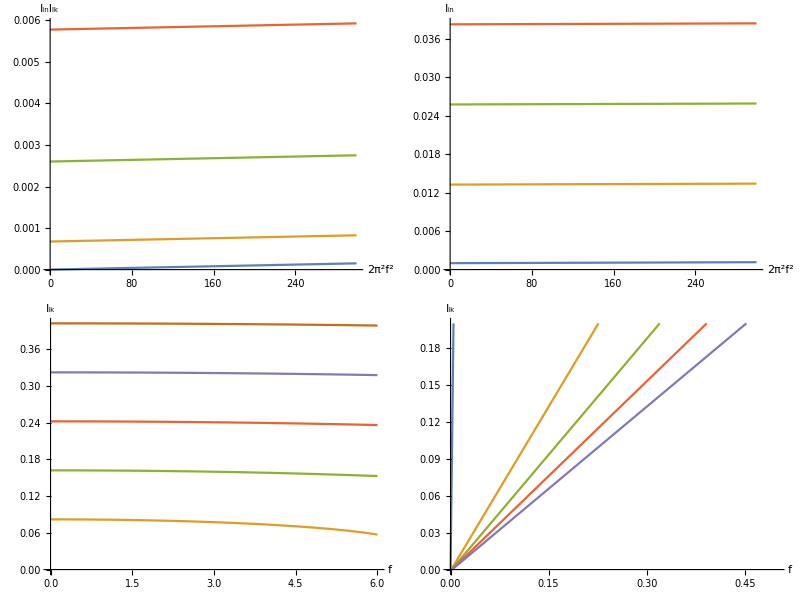

```mathematica
Grid[{{
Plot[{
calibFuncIinIlk[X,0.001, pquatmp, ptautmp, pilkrtmp],
calibFuncIinIlk[X,0.051, pquatmp, ptautmp, pilkrtmp],
calibFuncIinIlk[X,0.101, pquatmp, ptautmp, pilkrtmp],
calibFuncIinIlk[X,0.151, pquatmp, ptautmp, pilkrtmp]
},
{X, 0,300},AxesLabel->{"2π^2f^2","I_inI_lk"},ImageSize->Medium,PlotRange->All],
Plot[{
calibFuncIin[X,0.001, pquatmp, ptautmp, pilkrtmp],
calibFuncIin[X,0.051, pquatmp, ptautmp, pilkrtmp],
calibFuncIin[X,0.101, pquatmp, ptautmp, pilkrtmp],
calibFuncIin[X,0.151, pquatmp, ptautmp, pilkrtmp]
}
,{X, 0,300},AxesLabel->{"2π^2f^2","I_in"},ImageSize->Medium]},{
Plot[{
invcalibFuncIlk[f,0.001, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlk[f,0.021, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlk[f,0.041, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlk[f,0.061, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlk[f,0.081, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlk[f,0.101, pquatmp, ptautmp, pilkrtmp]
}
,{f, 0,6},AxesLabel->{"f","I_lk"},ImageSize->Medium],
Plot[{
invcalibFuncIlkiIn[f,0.50000001, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,0.500025, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,0.50005, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,0.500075, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,0.5001, pquatmp, ptautmp, pilkrtmp]
}
,{f, 0,0.5},AxesLabel->{"f","I_lk"},ImageSize->Medium,PlotRange->{0,0.2}]
}}]
```

#### Scatter plot of simulated data that describes the f^2 relation to I_in and I_lk (one common manipulator)

```mathematica
pquatmp=2;
ptautmp = 0.001;
pilkrtmp=0.008;
Manipulate[
iInRange=Range[0.5001,0.521,0.005];
IlkRange=Range[0.001,0.2,0.01];
IinRange=Range[0.001,0.1,0.005];
imgSize=Medium;

plotData1=Transpose[Table[{2 π^2 fFunc[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp]^2,iIntoIin[i,j,pquatmp,pilkrtmp]j},
{i,iInRange},{j,IlkRange}]];
plotData2=Transpose[Table[{2 π^2 fFunc[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp]^2,iIntoIin[i,j,pquatmp,pilkrtmp]},
{i,iInRange},{j,IlkRange}]];
plotData3=Table[{fFunc[i,j,pquatmp,ptautmp,pilkrtmp],j},
{i,IinRange},{j,IlkRange}];
plotData4=Table[{fFunc[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp],j},
{i,iInRange},{j,IlkRange}];
Grid[{
{ListPlot[plotData1,AxesLabel->{"2π^2f^2","I_inI_lk"},ImageSize->imgSize,PlotRange->{{0,1000},{0,0.015}}],
ListLogLogPlot[plotData1,AxesLabel->{"2π^2f^2","I_inI_lk"},ImageSize->imgSize,PlotRange->{{0.01,1000},{0.00001,Automatic}}]},
{ListPlot[plotData2,AxesLabel->{"2π^2f^2","I_in"},ImageSize->imgSize,PlotRange->{{0,1000},{0,Automatic}}],
ListLogLogPlot[plotData2,AxesLabel->{"2π^2f^2","I_in"},ImageSize->imgSize,PlotRange->{{0.01,1000},{0.001,Automatic}}]},
{Show[
ListPlot[plotData3,AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotRange->{0,0.2}],
Plot[{
IlkFunc[f,IinRange⟦1⟧,pquatmp,ptautmp,pilkrtmp],
IlkFunc[f,IinRange⟦2⟧,pquatmp,ptautmp,pilkrtmp],
IlkFunc[f,IinRange⟦3⟧,pquatmp,ptautmp,pilkrtmp],
},{f,0,25},AxesLabel->{"f","I_lk"}]],
Show[
ListLogLogPlot[plotData3,AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotRange->{0.0001,0.2}],
LogLogPlot[{
IlkFunc[f,IinRange⟦1⟧,pquatmp,ptautmp,pilkrtmp],
IlkFunc[f,IinRange⟦2⟧,pquatmp,ptautmp,pilkrtmp],
IlkFunc[f,IinRange⟦3⟧,pquatmp,ptautmp,pilkrtmp],
},{f,0.001,25},AxesLabel->{"f","I_lk"}]]},
{Show[
ListPlot[plotData4,AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotRange->{0,All},PlotRange->{{0,10},{0,0.2}}],
Plot[{
invcalibFuncIlkiIn[f,iInRange⟦1⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦2⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦3⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦4⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦5⟧, pquatmp, ptautmp, pilkrtmp]
}
,{f, 0,25},AxesLabel->{"f","I_lk"},ImageSize->Medium,PlotRange->{0,0.2},PlotStyle->Dashed]],
Show[
ListLogLogPlot[plotData4,AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotRange->{{0.01,10},{0.001,0.2}}],
LogLogPlot[{
invcalibFuncIlkiIn[f,iInRange⟦1⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦2⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦3⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦4⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦5⟧, pquatmp, ptautmp, pilkrtmp]
}
,{f, 0.00000001,25},AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotStyle->Dashed]]}
}],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}
]
```

#### Plot manipulator of simulated data of I_in I_lk as a function of 2 π^2 f^2

```mathematica
Grid[{
{
Manipulate[
plotData1=Transpose[Table[{2 π^2 fFunc[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp]^2,iIntoIin[i,j,pquatmp,pilkrtmp]j},
{i,iInRange},{j,IlkRange}]];
ListPlot[plotData1,AxesLabel->{"2π^2f^2","I_inI_lk"},ImageSize->imgSize,PlotRange->{{0,1000},{0,0.015}}],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}],
Manipulate[
plotData1=Transpose[Table[{2 π^2 fFunc[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp]^2,iIntoIin[i,j,pquatmp,pilkrtmp]j},
{i,iInRange},{j,IlkRange}]];
ListLogLogPlot[plotData1,AxesLabel->{"2π^2f^2","I_inI_lk"},ImageSize->imgSize,PlotRange->{{0.01,1000},{0.00001,Automatic}}],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}]
}}]
```

|

#### Plot manipulator of simulated data of I_in as a function of 2 π^2 f^2

```mathematica
Grid[{
{
Manipulate[
plotData2=Transpose[Table[{2 π^2 fFunc[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp]^2,iIntoIin[i,j,pquatmp,pilkrtmp]},
{i,iInRange},{j,IlkRange}]];
ListPlot[plotData2,AxesLabel->{"2π^2f^2","I_in"},ImageSize->imgSize,PlotRange->{{0,1000},{0,Automatic}}],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}],
Manipulate[
plotData2=Transpose[Table[{2 π^2 fFunc[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp]^2,iIntoIin[i,j,pquatmp,pilkrtmp]},
{i,iInRange},{j,IlkRange}]];
ListLogLogPlot[plotData2,AxesLabel->{"2π^2f^2","I_in"},ImageSize->imgSize,PlotRange->{{0.01,1000},{0.001,Automatic}}],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}]
}}]
```

|

#### Plot manipulator of simulated data of I_lk as a function of 2 π^2 f^2, varying I_in

```mathematica
Grid[{
{
Manipulate[
plotData3=Table[{fFunc[i,j,pquatmp,ptautmp,pilkrtmp],j},
{i,IinRange},{j,IlkRange}];
Show[
ListPlot[plotData3,AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotRange->{0,0.2}],
Plot[{
IlkFunc[f,IinRange⟦1⟧,pquatmp,ptautmp,pilkrtmp],
IlkFunc[f,IinRange⟦2⟧,pquatmp,ptautmp,pilkrtmp],
IlkFunc[f,IinRange⟦3⟧,pquatmp,ptautmp,pilkrtmp],
},{f,0,25},AxesLabel->{"f","I_lk"}]],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}],
Manipulate[
plotData3=Table[{fFunc[i,j,pquatmp,ptautmp,pilkrtmp],j},
{i,IinRange},{j,IlkRange}];
Show[
ListLogLogPlot[plotData3,AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotRange->{0.0001,0.2}],
LogLogPlot[{
IlkFunc[f,IinRange⟦1⟧,pquatmp,ptautmp,pilkrtmp],
IlkFunc[f,IinRange⟦2⟧,pquatmp,ptautmp,pilkrtmp],
IlkFunc[f,IinRange⟦3⟧,pquatmp,ptautmp,pilkrtmp],
},{f,0.001,25},AxesLabel->{"f","I_lk"}]],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}]
}}]
```

|

#### Plot manipulator of simulated data of I_lk as a function of 2 π^2 f^2, varying i_in

```mathematica
Grid[{
{
Manipulate[
plotData4=Table[{fFunc[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp],j},
{i,iInRange},{j,IlkRange}];
Show[
ListPlot[plotData4,AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotRange->{0,All},PlotRange->{{0,10},{0,0.2}}],
Plot[{
invcalibFuncIlkiIn[f,iInRange⟦1⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦2⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦3⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦4⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦5⟧, pquatmp, ptautmp, pilkrtmp]
}
,{f, 0,25},AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotRange->{0,0.2},PlotStyle->Dashed]],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}],
Manipulate[
plotData4=Table[{fFunc[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp],j},
{i,iInRange},{j,IlkRange}];
Show[
ListLogLogPlot[plotData4,AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotRange->{{0.01,10},{0.001,0.2}}],
LogLogPlot[{
invcalibFuncIlkiIn[f,iInRange⟦1⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦2⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦3⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦4⟧, pquatmp, ptautmp, pilkrtmp],
invcalibFuncIlkiIn[f,iInRange⟦5⟧, pquatmp, ptautmp, pilkrtmp]
}
,{f, 0.00000001,25},AxesLabel->{"f","I_lk"},ImageSize->imgSize,PlotStyle->Dashed]],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}]
}
}]
```

|

#### Compare actual firing rate (f(I_lk)) vs series-approximated firing rate (f̃(I_lk))

In the plots above, we see I_lk as a function of f̃, where f̃ is the calculated using the Taylor Series approximation of f^2.  To gain a little understanding and perhaps insight, I wanted to compare f̃ to f, where f is the actual firing rate as gotten from h(i_in).

```mathematica
pquatmp=2;
ptautmp = 0.001;
pilkrtmp=0.000;
iInRange=Range[0.5001,0.501,0.0001];
IlkRange=Range[0.00,0.2,0.005];
IinRange=Range[0.00,0.1,0.01];
Manipulate[
approxFData=Table[{j,fFunc[i,j,pquatmp,ptautmp,pilkrtmp]},
{i,IinRange},{j,IlkRange}];
accurFData=Table[{j,fFuncAccurate[i,j,pquatmp,ptautmp,pilkrtmp]},
{i,IinRange},{j,IlkRange}];
approxFEq=Table[fFunc[i,Ilk,pquatmp,ptautmp,pilkrtmp],{i,IinRange}];
accurFEq=Table[fFuncAccurate[i,Ilk,pquatmp,ptautmp,pilkrtmp],{i,IinRange}];
Show[
ListPlot[approxFData,AxesLabel->{"I_lk","f"},PlotMarkers->{"●",6},ImageSize->imgSize,PlotRange->{0,Automatic},ImageSize->Large],
ListPlot[accurFData,AxesLabel->{"I_lk","f"},PlotMarkers->{"●",6},ImageSize->imgSize,PlotRange->{0,Automatic}],
Plot[approxFEq,{Ilk,0.00,0.2},PlotStyle->Dashed,PlotRange->{0,All}],
Plot[accurFEq,{Ilk,0.00,0.2},PlotStyle->Line,PlotRange->{0,All}],
Plot[fFuncAccurate[iIntoIin[iIn,Ilk,pquatmp,pilkrtmp],Ilk,pquatmp,ptautmp,pilkrtmp],{Ilk,0.001,0.2},PlotRange->{0,All}],
ImageSize->Full
],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"},
{{iIn,0.501,"i_in"},0.5,2.0,0.001}
]
```

#### 3D Plot of relation of I_in and I_lk to (2 π^2 f^2)/I_lk

```mathematica
Plot3D[calibFunc[Iin,Ilk,2,0.001,0.003],{Iin,0.,1},{Ilk,0.001,0.25},
AxesLabel->{Iin,Ilk,f},Boxed->False]
```

-Graphics3D-

#### Manipulator to show dimensionless relationship between f^2, 1/(τ·(h(i_in))^2), and ⅆ/(ⅆ i_in)1/(h(i_in))^2

Use a manipulator to show that near bifurcation, f^2 is a linear function.  Note: As tau gets smaller, we need to be even closer to bifurcation for this approximation to still hold.

```mathematica
imgsz=600;
labelSz=15;
fFunc[tau_,iin_,a_]:=(1/(tau*hApprox[iin]))^a
dfFunc=D[1/hApprox[iin],iin];
dfFunc2=D[(1/hApprox[iin])^2,iin];
Manipulate[
Grid[{{
p1=Plot[{fFunc[tau,iin,1],fFunc[tau,iin,2]},{iin,0.5,xmax},
PlotRange->{{0.5,xmax},{0,ymax1}},
ImageSize->imgsz,
Axes->{True,False},
AxesLabel->{"i_in"}];,
Show[{p1,Graphics[Text["f",{(xmax-.002),2.5}]],Graphics[Text["f^2",{(xmax-.002),4.8}]]}],
Plot[{dfFunc2},{iin,0.5,1},
PlotRange->{{0.5,xmax},{ymin2,ymax2}},
ImageSize->imgsz,
AxesLabel->{"i_in","ⅆ/ⅆSubscriptBox[i, in]1/h[SubscriptBox[i, in]]"}]
}}],
{{tau,0.010,"τ"},0.001,0.100,0.001,Appearance->{"Open"}},
{{xmax,0.51,"x_max"},0.501,1,0.001,Appearance->{"Open"}},
{{ymax1,5,"y_max1"},1,1000,1,Appearance->{"Open"}},
{{ymin2,0,"y_min2"},0,1,0.001,Appearance->{"Open"}},
{{ymax2,0.2,"y_max2"},0.001,1,0.001,Appearance->{"Open"}}
]
```

### Manipulator for the series-expansion theory

This manipulator allows us to see how each parameter effects the theory.  From this manipulator, and from the math, it becomes clear that the x-intercept for any known I_lk is set by p_qua and p_ilkr.   The slope is set by p_tau and p_qua, where p_qua doesn’t affect where the y-intercept intersects, while p_tau doesn’t effect where the x-intercept intersects.  Changing I_lk only slides the curve up or down (or left or right...same difference).

```mathematica
Manipulate[
Plot[{calibFunc[Iin,Ilk,pqua,ptau,pilkr],calibFunc[Iin,pilkr,pqua,ptau,pilkr]},{Iin,0.,0.2},
AxesLabel->{Iin,"2π^2f^2/Ilk"},
PlotRange->{-10^5,4*10^5},
PlotStyle->{Red,Blue}],
{{Ilk,0.001},0.001,0.250,0.001, Appearance->"Open"},
{{pqua,1.5},0,2 ,0.01,Appearance->"Open"},
{{ptau,0.001},0.0005,0.0015, Appearance->"Open"},
{{pilkr,0.003},0.001,0.008 ,Appearance->"Open"}
]
```

### Show derivation for a cubic neuron of f^2∝i_in-2/3

```mathematica
fireTau3=1/Integrate[1/(1/3 im^3+iin-iinth),{im,0,∞},Assumptions-> iin>0.66,GenerateConditions->False]
```

(3 3^(1/6))/(2 π (1/(iin-iinth))^(2/3))

```mathematica
fireTau3^2
```

(9 3^(1/3))/(4 π^2 (1/(iin-iinth))^(4/3))

```mathematica
Series[fireTau3^2,{iin,0.666,1},Assumptions->{β0<1,βf>1}]
```

(9 3^(1/3))/(4 π^2 (1/(0.666-iinth))^(4/3))+(0.438391 (iin-0.666))/(1/(0.666-iinth))^(1/3)+O((iin-0.666)^2)

### 2^nd order approximation of f^2

#### Equation of 2^nd order approximation of f^2 in terms of I_in, I_lk, ρ_qua, ρ_tau, and ρ_ilkr

```mathematica
f^2==(Ilk+pilkr)^2/ptau^2 ft2Approx2[IintoiIn[Iin,Ilk,pqua,pilkr]]
```

f^2==((Ilk+pilkr)^2 (-(2 √2 (π^2-6) ((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)^(5/2))/(3 π^5)+(3 ((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)^2)/π^4+(√2 ((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)^(3/2))/π^3+((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)/(2 π^2)))/ptau^2

#### Plot the 2^nd order approximation of f^2 as a function of I_in and I_lk

```mathematica
IlkRange=Range[0.001,0.2,0.04];  (* temporary here to get less plots *)
```

```mathematica
Manipulate[
pltEqns2 = Table[(Ilk+pilkrManip)^2/ptauManip ft2Approx2[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
(*data3rdOrder=Transpose[Table[{iIntoIin[i,j,pquaManip,pilkrManip],2 π^2(j+pilkrManip)^2/ptauManip fireTau[i,0,∞]^2},
{i,Range[0.501,0.801,0.05]},{j,IlkRange}]];*)
data2ndOrder=Transpose[Table[{iIntoIin[i,j,pquaManip,pilkrManip],(j+pilkrManip)^2/ptauManip ft2[i]},
{i,Range[0.501,0.801,0.02]},{j,IlkRange}]];
pfull2=Plot[{pltEqns2},{Iin, 0,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Medium,PlotRange->{{0,Automatic},{0,Automatic}}];
Grid[{{
Show[
Plot[{pltEqns2},{Iin, 0,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Full,PlotRange->{{0,xmax},{0,ymax}},Epilog->Inset[pfull2,{0,ymax},{Left,Top}]],
ListPlot[data2ndOrder,AxesLabel->{"I_in","f^2"},ImageSize->Full,PlotRange->All]
]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"},
{xmax,0.08},
{ymax,2}
]
```

#### LogLogPlot the 2^nd order approximation of f^2 as a function of I_in and I_lk

```mathematica
IlkRange=Range[0.001,0.2,0.04];  (* temporary here to get less plots *)
```

```mathematica
Manipulate[
pltEqns2 = Table[((Ilk+pilkrManip)^2/ptauManip)ft2Approx2[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
(*data3rdOrder=Transpose[Table[{iIntoIin[i,j,pquaManip,pilkrManip],2 π^2((j+pilkrManip)^2/ptauManip)fireTau[i,0,∞]^2},
{i,Range[0.501,0.801,0.05]},{j,IlkRange}]];*)
data2ndOrder=Transpose[Table[{iIntoIin[i,j,pquaManip,pilkrManip],((j+pilkrManip)^2/ptauManip)ft2[i]},
{i,Range[0.501,0.801,0.05]},{j,IlkRange}]];
pfull2=LogLogPlot[{pltEqns2},{Iin, 0.001,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Medium,PlotRange->{{0.001,Automatic},{0.001,Automatic}}];
Grid[{{
Show[
LogLogPlot[{pltEqns2},{Iin, 0.001,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Full,PlotRange->{{0.001,xmax},{0.0000001,ymax}},Epilog->Inset[pfull,{0.00001,ymax},{Left,Top}]],
ListLogLogPlot[data2ndOrder,AxesLabel->{"I_in","f^2"},ImageSize->Full,PlotRange->All]
]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"},
{xmax,0.3},
{ymax,5}
]
```

#### Contour Plot of the 2nd order approximation of f^2 as a function of I_in and I_lk

```mathematica
Manipulate[
pltEqns2 = Table[((Ilk+pilkrManip)^2/ptauManip)ft2Approx2[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
Grid[{{
Show[
ContourPlot[((Ilk+pilkrManip)^2/ptauManip)ft2Approx2[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],
{Ilk, 0,0.2},{Iin, 0,0.3},FrameLabel->{"I_lk","I_in"},ImageSize->Medium,PlotRange->{0,Automatic},ContourLabels->All,RegionFunction->Function[{Ilk,Iin},IintoiIn[Iin,Ilk,pquaManip,pilkrManip]<π]],
Plot[{
iIntoIin[1/2,Ilk,pquaManip,pilkrManip],
iIntoIin[0.8,Ilk,pquaManip,pilkrManip],
iIntoIin[π,Ilk,pquaManip,pilkrManip]},
{Ilk,0.002,0.2}]
]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}
]
```

#### 3D Plot of the 2^nd order approximation of f^2 as a function of I_in and I_lk

```mathematica
Manipulate[
pltEqns2 = Table[((Ilk+pilkrManip)^2/ptauManip)ft2Approx2[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
Grid[{{
Plot3D[((Ilk+pilkrManip)^2/ptauManip)ft2Approx2[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],
{Iin, 0,0.3},{Ilk, 0,0.2},AxesLabel->{"I_in","I_lk","f^2"},ImageSize->Medium,PlotRange->{0,Automatic},RegionFunction->Function[{Iin,Ilk},IintoiIn[Iin,Ilk,pquaManip,pilkrManip]<π]]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}
]
```

#### All 2^nd order approximation plots of f^2 as a function of I_in and I_lk

```mathematica
Manipulate[
pltEqns2 = Table[((Ilk+pilkrManip)^2/ptauManip)ft2Approx2[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
Ilks=Table[Ilk,{Ilk,IlkRange}];
Grid[{{
Show[
Plot[{pltEqns2},
{Iin, 0,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Medium,PlotRange->{0,Automatic}]
]
},{
Show[
ContourPlot[((Ilk+pilkrManip)^2/ptauManip)ft2Approx2[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],
{Iin, 0,0.3},{Ilk, 0,0.2},FrameLabel->{"I_in","I_lk"},ImageSize->Medium,PlotRange->{0,Automatic},ContourLabels->All,RegionFunction->Function[{Iin,Ilk},IintoiIn[Iin,Ilk,pquaManip,pilkrManip]<π]],
Plot[Ilks,{Iin,0,0.3},PlotStyle->{Dashed}]
]
},{
Plot3D[((Ilk+pilkrManip)^2/ptauManip)ft2Approx2[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],
{Iin, 0,0.3},{Ilk, 0,0.2},AxesLabel->{"I_in","I_lk","f^2"},ImageSize->Medium,PlotRange->{0,Automatic},
RegionFunction->Function[{Iin,Ilk},IintoiIn[Iin,Ilk,pquaManip,pilkrManip]<π]]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}
]
```

```mathematica
Table[Ilk,{Ilk,IlkRange}]
```

{0.001,0.041,0.081,0.121,0.161}

### 3^rd order approximation of f^2

#### Equation of 3^rd order approximation of f^2 in terms of I_in, I_lk, ρ_qua, ρ_tau, and ρ_ilkr

```mathematica
f^2==(Ilk+pilkr)^2/ptau^2 ft2Approx3[IintoiIn[Iin,Ilk,pqua,pilkr]]
```

f^2==1/ptau^2(Ilk+pilkr)^2 ((4 √2 (15-10 π^2+π^4) ((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)^(7/2))/(5 π^7)+(10/π^6-4/π^4) ((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)^3-(2 √2 (π^2-6) ((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)^(5/2))/(3 π^5)+(3 ((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)^2)/π^4+(√2 ((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)^(3/2))/π^3+((Iin Ilk pqua)/(Ilk+pilkr)^2-0.5)/(2 π^2))

#### Plot the 3^rd order approximation of f^2 as a function of I_in and I_lk

```mathematica
IlkRange=Range[0.001,0.2,0.04];  (* temporary here to get less plots *)
```

```mathematica
Manipulate[
pltEqns = Table[(Ilk+pilkrManip)^2/ptauManip ft2Approx3[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
(*data3rdOrder=Transpose[Table[{iIntoIin[i,j,pquaManip,pilkrManip],2 π^2(j+pilkrManip)^2/ptauManip fireTau[i,0,∞]^2},
{i,Range[0.501,0.801,0.05]},{j,IlkRange}]];*)
data3rdOrder=Transpose[Table[{iIntoIin[i,j,pquaManip,pilkrManip],(j+pilkrManip)^2/ptauManip ft2[i]},
{i,Range[0.501,0.801,0.05]},{j,IlkRange}]];
pfull=Plot[{pltEqns},{Iin, 0,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Medium,PlotRange->{{0,Automatic},{0,Automatic}}];
Grid[{{
Show[
Plot[{pltEqns},{Iin, 0,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Full,PlotRange->{{0,xmax},{0,ymax}},Epilog->Inset[pfull,{0,ymax},{Left,Top}]],
ListPlot[data3rdOrder,AxesLabel->{"I_in","f^2"},ImageSize->Full,PlotRange->All]
]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"},
{xmax,0.08},
{ymax,2}
]
```

#### LogLogPlot the 3^rd order approximation of f^2 as a function of I_in and I_lk

```mathematica
IlkRange=Range[0.001,0.2,0.04];  (* temporary here to get less plots *)
```

```mathematica
Manipulate[
pltEqns = Table[(Ilk+pilkrManip)^2/ptauManip ft2Approx3[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
(*data3rdOrder=Transpose[Table[{iIntoIin[i,j,pquaManip,pilkrManip],2 π^2(j+pilkrManip)^2/ptauManip fireTau[i,0,∞]^2},
{i,Range[0.501,0.801,0.05]},{j,IlkRange}]];*)
data3rdOrder=Transpose[Table[{iIntoIin[i,j,pquaManip,pilkrManip],(j+pilkrManip)^2/ptauManip ft2[i]},
{i,Range[0.501,0.801,0.05]},{j,IlkRange}]];
pfull=LogLogPlot[{pltEqns},{Iin, 0.001,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Medium,PlotRange->{{0.001,Automatic},{0.001,Automatic}}];
Grid[{{
Show[
LogLogPlot[{pltEqns},{Iin, 0.001,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Full,PlotRange->{{0.001,xmax},{0.0000001,ymax}},Epilog->Inset[pfull,{0.00001,ymax},{Left,Top}]],
ListLogLogPlot[data3rdOrder,AxesLabel->{"I_in","f^2"},ImageSize->Full,PlotRange->All]
]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"},
{xmax,0.3},
{ymax,5}
]
```

#### Contour Plot of the 3rd order approximation of f^2 as a function of I_in and I_lk

```mathematica
Manipulate[
pltEqns = Table[(Ilk+pilkrManip)^2/ptauManip ft2Approx3[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
Grid[{{
Show[
ContourPlot[(Ilk+pilkrManip)^2/ptauManip ft2Approx3[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],
{Ilk, 0,0.2},{Iin, 0,0.3},FrameLabel->{"I_lk","I_in"},ImageSize->Medium,PlotRange->{0,Automatic},ContourLabels->All,RegionFunction->Function[{Ilk,Iin},IintoiIn[Iin,Ilk,pquaManip,pilkrManip]<π]],
Plot[{
iIntoIin[1/2,Ilk,pquaManip,pilkrManip],
iIntoIin[0.8,Ilk,pquaManip,pilkrManip],
iIntoIin[π,Ilk,pquaManip,pilkrManip]},
{Ilk,0.002,0.2}]
]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}
]
```

#### 3D Plot of the 3rd order approximation of f^2 as a function of I_in and I_lk

```mathematica
Manipulate[
pltEqns = Table[(Ilk+pilkrManip)^2/ptauManip ft2Approx3[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
Grid[{{
Plot3D[(Ilk+pilkrManip)^2/ptauManip ft2Approx3[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],
{Iin, 0,0.3},{Ilk, 0,0.2},AxesLabel->{"I_in","I_lk","f^2"},ImageSize->Medium,PlotRange->{0,Automatic},RegionFunction->Function[{Iin,Ilk},IintoiIn[Iin,Ilk,pquaManip,pilkrManip]<π]]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}
]
```

#### All 3rd order approximation plots of f^2 as a function of I_in and I_lk

```mathematica
Manipulate[
pltEqns = Table[(Ilk+pilkrManip)^2/ptauManip ft2Approx3[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],{Ilk,IlkRange}];
Ilks=Table[Ilk,{Ilk,IlkRange}];
Grid[{{
Show[
Plot[{pltEqns},
{Iin, 0,0.3},AxesLabel->{"I_in","f^2"},ImageSize->Medium,PlotRange->{0,Automatic}]
]
},{
Show[
ContourPlot[(Ilk+pilkrManip)^2/ptauManip ft2Approx3[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],
{Iin, 0,0.3},{Ilk, 0,0.2},FrameLabel->{"I_in","I_lk"},ImageSize->Medium,PlotRange->{0,Automatic},ContourLabels->All,RegionFunction->Function[{Iin,Ilk},IintoiIn[Iin,Ilk,pquaManip,pilkrManip]<π]],
Plot[Ilks,{Iin,0,0.3},PlotStyle->{Dashed}]
]
},{
Plot3D[(Ilk+pilkrManip)^2/ptauManip ft2Approx3[IintoiIn[Iin,Ilk,pquaManip,pilkrManip]],
{Iin, 0,0.3},{Ilk, 0,0.2},AxesLabel->{"I_in","I_lk","f^2"},ImageSize->Medium,PlotRange->{0,Automatic},
RegionFunction->Function[{Iin,Ilk},IintoiIn[Iin,Ilk,pquaManip,pilkrManip]<π]]
}}],
{{pquaManip,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptauManip,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrManip,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}
]
```

```mathematica
Table[Ilk,{Ilk,IlkRange}]
```

{0.001,0.041,0.081,0.121,0.161}

## Theory behind T^2

(THIS SECTION WAS ONLY THEORIZED AND NEVER IMPLEMENTED IN PYTHON BECAUSE THE ANALYSIS OF THE MATH BELOW SHOWED THAT NEAR BIFURCATION THE PERIOD WOULD NOT HELP WITH RESOLVING ρ_tau)

This section will help show some of the math and intuition behind what happens to the circuit when you square the period (as opposed to the firing rate).  A lot of these plots should be inverses of the previous section (Theory behind f^2), but to be thorough and complete, I want to model all of the approximations

### Show derivation of T^2≈τ^2· h̃(i_in), where h̃(i_in) is a series approximation of h(i_in)

```mathematica
T[iin_,τ_]:=τ hApprox[iin]
TSqApprox[iin_,τ_]:=τ^2 Series[(hApprox[iin])^2,{iin,0.5,1}]
T[iin,τ]
TSqApprox[iin,τ]
```

(τ (2 cot^-1(√(2 iin-1))+π))/(√(2 iin-1))

(2 π^2 τ^2)/(iin-0.5)-(4 (√2 π τ^2))/(√(iin-0.5))+4 τ^2+8/3 √2 π √(iin-0.5) τ^2-16/3 (iin-0.5) τ^2+O((iin-0.5)^(3/2))

Out of curiosity, wanted to see how the h function is directly approximated by Taylor Series

```mathematica
Series[(hApprox[iin]),{iin,0.5,1}]
```

(√2 π)/(√(iin-0.5))-2+(4 (iin-0.5))/3+O((iin-0.5)^(3/2))

### Approximate the error that results from using the series expansion

#### Approximate accuracy of the first order approximation compared to the actual (h(i_in))^2 value

```mathematica
errorT0[iin_]:=Abs[hApprox[iin]^2-((2 π^2)/(iin-0.5))]/hApprox[iin]^2
errorT1[iin_]:=Abs[hApprox[iin]^2-((2 π^2)/(iin-0.5)-(8π)/(√(2iin -1))+4+(8π)/3 √(2 iin-1)-16/3(iin-0.5))]/hApprox[iin]^2
errorT1Approx[iin_]:=Abs[hApprox[iin]^2-((2 π^2)/(iin-0.5)-(8π)/(√(2iin -1))+4)]/hApprox[iin]^2
```

```mathematica
Manipulate[
Grid[{{
Text[errorT0[iin]*100"%"],
Text[errorT1[iin]*100"%"],
Text[errorT1Approx[iin]*100"%"]
}}],
{{iin,0.520,"i_in"},0.5,0.55,.001,Appearance->"Open"}
]
```

```mathematica
hApprox[iin]^2
```

((2 cot^-1(√(2 iin-1))+π)^2)/(2 iin-1)

```mathematica
percError = Range[0.01,0.20,0.01];
Grid[{{
{#,NSolve[((2 π^2)/(iin-0.5)-hApprox[iin]^2)/hApprox[iin]^2==# ,iin]}&/@percError
}}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

(0.01 | {{iin→0.500122}}
0.02 | {{iin→0.500479}}
0.03 | {{iin→0.501064}}
0.04 | {{iin→0.501866}}
0.05 | {{iin→0.502877}}
0.06 | {{iin→0.504091}}
0.07 | {{iin→0.5055}}
0.08 | {{iin→0.507099}}
0.09 | {{iin→0.508881}}
0.1 | {{iin→0.510842}}
0.11 | {{iin→0.512976}}
0.12 | {{iin→0.51528}}
0.13 | {{iin→0.51775}}
0.14 | {{iin→0.520382}}
0.15 | {{iin→0.523172}}
0.16 | {{iin→0.526119}}
0.17 | {{iin→0.529219}}
0.18 | {{iin→0.53247}}
0.19 | {{iin→0.53587}}
0.2 | {{iin→0.539416}})

### Solve for T^2 vs I_in and I_lk

#### Solve using less accurate Taylor series approximation of h(i_in)

```mathematica
FullSimplify[T^2==(ptau/(Ilk+pilkr))^2(2 π^2)/((pqua Iin Ilk)/(Ilk+ pilkr)^2-1/2)]
FullSimplify[Solve[T^2==-(4 π^2 ptau^2)/((Ilk+pilkr)^2-2 Y Ilk pqua),Y]]
FullSimplify[Solve[T^2==-(4 π^2 ptau^2)/((Ilk+pilkr)^2-2 Y pqua),Y]]
```

T^2==-(4 π^2 ptau^2)/((Ilk+pilkr)^2-2 Iin Ilk pqua)

{{Y→(T^2 (Ilk+pilkr)^2+4 π^2 ptau^2)/(2 Ilk pqua T^2)}}

{{Y→(T^2 (Ilk+pilkr)^2+4 π^2 ptau^2)/(2 pqua T^2)}}

### Visual understanding of this theory for calibration

T^2= (2π ρ_tau)^2/(2 ρ_qua I_in I_lk-(I_lk+ρ_ilkr)^2)
1/(I_in I_lk)=(2 ρ_qua T^2)/((2π ρ_tau)^2+(T^2(I_lk+ρ_ilkr))^2)

#### Define equations for this calibration process

```mathematica
TFunc[Iin_,Ilk_,pqua_,ptau_,pilkr_]:=√((2π ptau)^2/(2pqua Iin Ilk-(Ilk+pilkr)^2))
TSq[Iin_,Ilk_,pqua_,ptau_,pilkr_]:=(2π ptau)^2/(2pqua Iin Ilk-(Ilk+pilkr)^2)
TSqY[X_,Ilk_,pqua_,ptau_,pilkr_]:=(2π ptau)^2/(2pqua X-(Ilk+pilkr)^2)
TinvIinIlk[T_,Ilk_,pqua_,ptau_,pilkr_]:=(2pqua T^2)/((2π ptau)^2+T^2(Ilk+pilkr)^2)
TinvIinIlkY[X_,Ilk_,pqua_,ptau_,pilkr_]:=(2pqua X)/((2π ptau)^2+X(Ilk+pilkr)^2)
TinvIin[T_,Ilk_,pqua_,ptau_,pilkr_]:=(2pqua Ilk T^2)/((2π ptau)^2+T^2(Ilk+pilkr)^2)
TinvIinY[X_,Ilk_,pqua_,ptau_,pilkr_]:=(2pqua Ilk X)/((2π ptau)^2+X(Ilk+pilkr)^2)
TinvIlk[T_,Iin_,pqua_,ptau_,pilkr_]:=T/(√((pqua Iin)^2 T^2-2 pilkr pqua Iin T^2-(2π ptau)^2)-T(pilkr-pqua Iin))
TIlkiIn[T_,iIn_,pqua_,ptau_,pilkr_]:=(2π ptau)/(T √(2 iIn -1))-pilkr
TinvIlkiIn[T_,iIn_,pqua_,ptau_,pilkr_]:=(T √(2 iIn -1))/(2π ptau -pilkr T √(2 iIn -1))
IintoiIn[Iin_,Ilk_,pqua_,pilkr_]:=pqua (Iin Ilk)/(Ilk+pilkr)^2
iIntoIin[iIn_,Ilk_,pqua_,pilkr_]:=(iIn (Ilk+pilkr)^2)/(pqua Ilk)
```

#### Global Variables

Define ranges and image size variables for use with the plots below

```mathematica
pquatmp=2;
ptautmp = 0.001;
pilkrtmp=0.001;
iInRange=Range[0.501,0.521,0.005];
IlkRange=Range[0.001,0.2,0.01];
IinRange=Range[0.001,0.1,0.005];
ptauoffset=0.0015;
imgSize=Large;
```

#### Plot of T^2 as a function of I_in I_lk

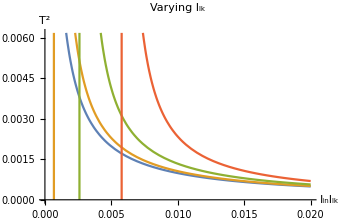

```mathematica
Grid[{{
Plot[{
TSqY[X,0.001, pquatmp, ptautmp, pilkrtmp],
TSqY[X,0.051, pquatmp, ptautmp, pilkrtmp],
TSqY[X,0.101, pquatmp, ptautmp, pilkrtmp],
TSqY[X,0.151, pquatmp, ptautmp, pilkrtmp]
},
{X, 0.000001,0.02},PlotLabel->"Varying I_lk",AxesLabel->{"I_inI_lk","T^2"},ImageSize->Medium,PlotRange->{0,Automatic}]
}}]
```

#### Plot of T^2 as a function of I_in

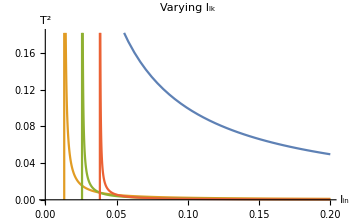

```mathematica
Grid[{{
Plot[{
TSq[Iin,0.001, pquatmp, ptautmp, pilkrtmp],
TSq[Iin,0.051, pquatmp, ptautmp, pilkrtmp],
TSq[Iin,0.101, pquatmp, ptautmp, pilkrtmp],
TSq[Iin,0.151, pquatmp, ptautmp, pilkrtmp]
},
{Iin, 0.002,0.2},PlotLabel->"Varying I_lk",AxesLabel->{"I_in","T^2"},ImageSize->Medium,PlotRange->{0,Automatic}]
}}]
```

#### Plot of 1/(I_in I_lk) as a function of T^2

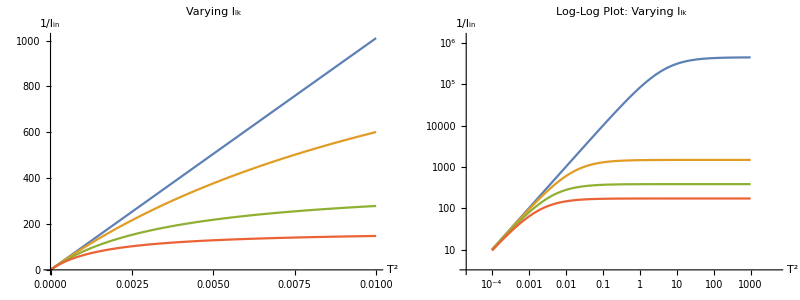

```mathematica
Grid[{{
Plot[{
TinvIinIlkY[X,0.002, pquatmp, ptautmp, pilkrtmp],
TinvIinIlkY[X,0.051, pquatmp, ptautmp, pilkrtmp],
TinvIinIlkY[X,0.101, pquatmp, ptautmp, pilkrtmp],
TinvIinIlkY[X,0.151, pquatmp, ptautmp, pilkrtmp]
},{X, 0,0.01},PlotLabel->"Varying I_lk",AxesLabel->{"T^2","1/I_in"},ImageSize->Medium,PlotRange->{0,Automatic}],
LogLogPlot[{
TinvIinIlkY[X,0.002, pquatmp, ptautmp, pilkrtmp],
TinvIinIlkY[X,0.051, pquatmp, ptautmp, pilkrtmp],
TinvIinIlkY[X,0.101, pquatmp, ptautmp, pilkrtmp],
TinvIinIlkY[X,0.151, pquatmp, ptautmp, pilkrtmp]
},{X, 0.0001,1000.01},PlotLabel->"Log-Log Plot: Varying I_lk",AxesLabel->{"T^2","1/I_in"},ImageSize->Medium]
}
}]
```

#### Plot manipulator of simulated data of 1/(I_in I_lk) as a function of T^2

```mathematica
Grid[{
{
Manipulate[
plotData1=Transpose[Table[{TSq[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp],1/(iIntoIin[i,j,pquatmp,pilkrtmp]j)},
{i,iInRange},{j,IlkRange}]];
TinvIinIlkYFitEqs=Table[TinvIinIlkY[X,j, pquatmp, ptautmp, pilkrtmp],{j,IlkRange}];
plotData2=Transpose[Table[{TSq[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp+ptauoffset,pilkrtmp],1/(iIntoIin[i,j,pquatmp,pilkrtmp]j)},
{i,iInRange},{j,IlkRange}]];
TinvIinIlkYFitEqs2=Table[TinvIinIlkY[X,j, pquatmp, ptautmp+ptauoffset, pilkrtmp],{j,IlkRange}];
Show[
ListPlot[plotData1,AxesLabel->{"T^2","1/(I_inI_lk)"},ImageSize->imgSize,PlotRange->{{0,xmax},All},PlotMarkers->{"•"}],
ListPlot[plotData2,AxesLabel->{"T^2","1/(I_inI_lk)"},ImageSize->imgSize,PlotRange->{{0,xmax},All},PlotMarkers->{"◆"}],
Plot[{TinvIinIlkYFitEqs},{X,0,Max[plotData1⟦;;,;;,1⟧]},PlotStyle->Dashed,PlotRange->{{0,xmax},All}],
Plot[{TinvIinIlkYFitEqs2},{X,0,Max[plotData2⟦;;,;;,1⟧]},PlotStyle->Dashed,PlotRange->{{0,xmax},All}]
],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"},
{{xmax,Max[plotData1⟦;;,;;,1⟧],"x_max"},1,Max[{Max[plotData1⟦;;,;;,1⟧],Max[plotData2⟦;;,;;,1⟧]}],Appearance->"Open"}]
}
}]
```

```mathematica
{0.501,0.506,0.511,0.516,0.521}
```

{0.501,0.506,0.511,0.516,0.521}

#### Log-Log Plot manipulator of simulated data of 1/(I_in I_lk) as a function of T^2

```mathematica
Grid[{
{
Manipulate[
plotData1=Transpose[Table[{TSq[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp,pilkrtmp],1/(iIntoIin[i,j,pquatmp,pilkrtmp]j)},
{i,iInRange},{j,IlkRange}]];
TinvIinIlkYFitEqs=Table[TinvIinIlkY[X,j, pquatmp, ptautmp, pilkrtmp],{j,IlkRange}];
plotData2=Transpose[Table[{TSq[iIntoIin[i,j,pquatmp,pilkrtmp],j,pquatmp,ptautmp+ptauoffset,pilkrtmp],1/(iIntoIin[i,j,pquatmp,pilkrtmp]j)},
{i,iInRange},{j,IlkRange}]];
TinvIinIlkYFitEqs2=Table[TinvIinIlkY[X,j, pquatmp, ptautmp+ptauoffset, pilkrtmp],{j,IlkRange}];
Show[
ListLogLogPlot[plotData1,AxesLabel->{"T^2","1/I_inI_lk"},ImageSize->imgSize,PlotRange->All],ListLogLogPlot[plotData2,AxesLabel->{"T^2","1/(I_inI_lk)"},ImageSize->imgSize,PlotRange->All,PlotMarkers->{"◆"}],
LogLogPlot[{TinvIinIlkYFitEqs},{X,Min[plotData1⟦;;,;;,1⟧],Max[plotData2⟦;;,;;,1⟧]},PlotStyle->Dashed,PlotRange->All],
LogLogPlot[{TinvIinIlkYFitEqs2},{X,Min[plotData1⟦;;,;;,1⟧],Max[plotData2⟦;;,;;,1⟧]},PlotStyle->Dashed,PlotRange->All]
],
{{pquatmp,2,"ρ_qua"},0.5,4,0.001,Appearance->"Open"},
{{ptautmp,0.001,"ρ_tau"},0.0001,0.002,0.0001,Appearance->"Open"},
{{pilkrtmp,0.008,"ρ_ilkr"},0.0005,0.015,0.0001,Appearance->"Open"}]
}
}]
```

#### Plot of 1/I_in as a function of T^2

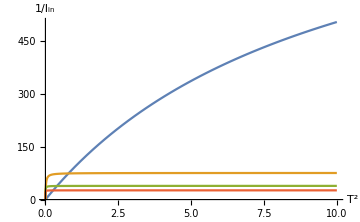

```mathematica
Grid[{{
Plot[{
TinvIinY[X,0.001, pquatmp, ptautmp, pilkrtmp],
TinvIinY[X,0.051, pquatmp, ptautmp, pilkrtmp],
TinvIinY[X,0.101, pquatmp, ptautmp, pilkrtmp],
TinvIinY[X,0.151, pquatmp, ptautmp, pilkrtmp]
},{X, 0,10},AxesLabel->{"T^2","1/I_in"},ImageSize->Medium]
}}]
```

#### Plot of 1/I_lk as a function of T

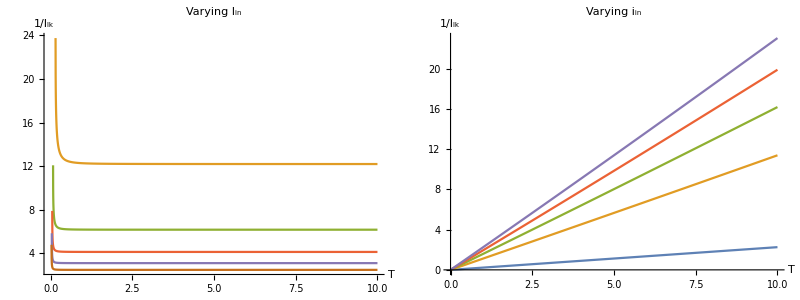

```mathematica
Grid[{{
Plot[{
TinvIlk[T,0.001, pquatmp, ptautmp, pilkrtmp],
TinvIlk[T,0.021, pquatmp, ptautmp, pilkrtmp],
TinvIlk[T,0.041, pquatmp, ptautmp, pilkrtmp],
TinvIlk[T,0.061, pquatmp, ptautmp, pilkrtmp],
TinvIlk[T,0.081, pquatmp, ptautmp, pilkrtmp],
TinvIlk[T,0.101, pquatmp, ptautmp, pilkrtmp]
}
,{T, 0,10},PlotLabel->"Varying I_in",AxesLabel->{"T","1/I_lk"},ImageSize->Medium],
Plot[{
TinvIlkiIn[T,0.500001, pquatmp, ptautmp, pilkrtmp],
TinvIlkiIn[T,0.500025, pquatmp, ptautmp, pilkrtmp],
TinvIlkiIn[T,0.50005, pquatmp, ptautmp, pilkrtmp],
TinvIlkiIn[T,0.500075, pquatmp, ptautmp, pilkrtmp],
TinvIlkiIn[T,0.5001, pquatmp, ptautmp, pilkrtmp]
},{T, 0,10},PlotLabel->"Varying i_in",AxesLabel->{"T","1/I_lk"},ImageSize->Medium,PlotRange->{0,Automatic}]
}}]
```

#### Plot of I_lk as a function of T

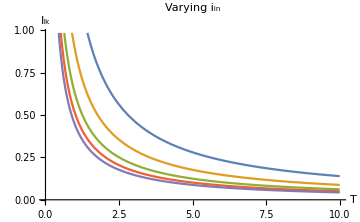

```mathematica
Grid[{{
Plot[{
TIlkiIn[T,0.50001, pquatmp, ptautmp, pilkrtmp],
TIlkiIn[T,0.500025, pquatmp, ptautmp, pilkrtmp],
TIlkiIn[T,0.50005, pquatmp, ptautmp, pilkrtmp],
TIlkiIn[T,0.500075, pquatmp, ptautmp, pilkrtmp],
TIlkiIn[T,0.5001, pquatmp, ptautmp, pilkrtmp]
}
,{T, 0,10},PlotLabel->"Varying i_in",AxesLabel->{"T","I_lk"},ImageSize->Medium,PlotRange->{0,Automatic}]
}}]
```

#### 3D plot manipulator of T^2 as a function of I_in and I_lk

```mathematica
Manipulate[
Plot3D[TSq[Iin,Ilk,pqua,ptau, pilkr],{Iin,0.,0.1},{Ilk,0.00,0.1},
AxesLabel->{"I_in","I_lk","T^2"},Boxed->False, ImageSize->Large,PlotRange->{0,10}],
{{pqua,2,"p_qua"},0,3.5,0.01,Appearance->{"Open"}},
{{ptau,0.001,"p_tau"},0.0005,0.0015,0.0001,Appearance->{"Open"}},
{{pilkr,0.008,"p_ilkr"},0.00005,0.015,0.00001,Appearance->{"Open"}}
]
```

## Appendix/Scratchwork

### Playing with some equations related to integrating the quadratic dynamical system equation

```mathematica
τ Integrate[1/(-im +1/2 im^2+iin),{im,0,∞},Assumptions-> iin>0.5]
τ Integrate[1/(-im +1/2 im^2+iin),{im,β,∞},Assumptions-> iin>0.5]
foo[iin_,Ilk_,ρIm0_,ρtau_,pilkr_]=ρtau/(Ilk+pilkr) Integrate[1/(-im +1/2 im^2+iin),{im,ρIm0/(Ilk+pilkr),∞},Assumptions-> iin>0.5,GenerateConditions->False]
```

(τ (2 cot^-1(√(2 iin-1))+π))/(√(2 iin-1))

(τ (π-2 tan^-1((β-1)/(√(2 iin-1)))))/(√(2 iin-1))

(ρtau (2 tan^-1((Ilk+pilkr-ρIm0)/(√(2 iin-1) (Ilk+pilkr)))+π))/(√(2 iin-1) (Ilk+pilkr))

```mathematica
Manipulate[
Grid[{
{
Grid[{{"τ_soma: ", N[ptau/Ilktemp]}}],
Grid[{{"Error@i_in=x_max: ", N[1/foo[xmax,Ilktemp,pIm0,ptau,pilkr]-1/foo[xmax,Ilktemp,0,ptau,pilkr]]}}]
},
{
Plot[{1/foo[iin,Ilktemp,0,ptau,pilkr],1/foo[iin,Ilktemp,pIm0,ptau,pilkr]},{iin,0.50001,xmax},
AxesOrigin->{0,0},
ImageSize->imSz,
PlotRange->{0,ymax1}],
Plot[{1/foo[iin,Ilktemp,pIm0,ptau,pilkr]-1/foo[iin,Ilktemp,0,ptau,pilkr]},{iin,0.50001,xmax},
AxesOrigin->{0,0},
ImageSize->imSz,
PlotRange->{0,ymax2}]

}
}
],
{{Ilktemp,0.05,"I_lk"},0.01,1,0.01,Appearance->{"Labeled","Open"}},
{{pIm0,0.0010,"ρ_Im0"},0.0001,0.01,0.0001,Appearance->{"Labeled","Open"}},
{{ptau,0.0010,"ρ_tau"},0.0001,0.01,0.0001,Appearance->{"Labeled","Open"}},
{{pilkr,0.0010,"ρ_ilkr"},0.0001,0.01,0.0001,Appearance->{"Labeled","Open"}},
{{xmax,10,"x_max"},1,50,1,Appearance->{"Labeled","Open"}},
{{ymax1,20,"y_max1"},1,500,1,Appearance->{"Labeled","Open"}},
{{ymax2,0.2,"y_max2"},0,5,0.1,Appearance->{"Labeled","Open"}},
{{imSz,350,"Image Size"},200,1000,50,Appearance->{"Labeled","Open"}}
]
```

```mathematica
Integrate[1/(im^2+iin),{im,β0,βf},GenerateConditions->False]
Integrate[1/(1/2 im^2+iin),{im,β0,βf},GenerateConditions->False]
Integrate[1/(-im+1/2 im^2+iin),{im,β0,βf},Assumptions-> iin>0.5,GenerateConditions->False]
```

(tan^-1(βf/(√iin))-tan^-1(β0/(√iin)))/(√iin)

(√2 (tan^-1(βf/(√2 √iin))-tan^-1(β0/(√2 √iin))))/(√iin)

(2 (tan^-1((βf-1)/(√(2 iin-1)))-tan^-1((β0-1)/(√(2 iin-1)))))/(√(2 iin-1))

### Understanding of roots as they are plotted

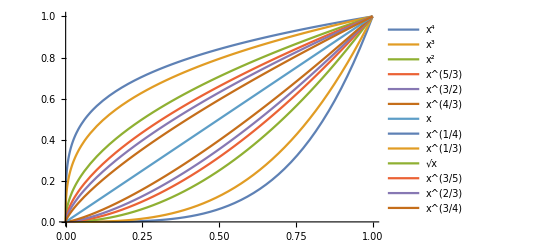

```mathematica
expEqs=Table[x^a,{a,{4/1,3/1,2/1,5/3,3/2,4/3,1/1}}];
expEqs1=Table[x^a,{a,{1/4,1/3,1/2,3/5,2/3,3/4}}];
Show[
Plot[{expEqs},{x,0,1}, PlotLegends->"Expressions"],
Plot[{expEqs1},{x,0,1}, PlotLegends->"Expressions"]
]
```

### Play section

```mathematica
pquatmp=2.9999389184
ptautmp=0.000997166345266
pilkrtmp=0.000127767073947
```

```mathematica
(Ilk+pilkrtmp)^2/ptautmp ft2Approx3[IintoiIn[0.02870431,0.172,pquatmp,pilkrtmp]]
```

(-8.48874-4.15239 ⅈ) (Ilk+0.008)^2